## Goals

Summarized from Slack Thread 15-17 July 2024

This is comprised of small amount of data  5x (vesicles + same volume), 10x (no vesicles + same volume)—“a set of duplicates”, and  5x (no vesicles + variable volume).  The 5 examples are at some discrete pHs.

Modeling goals: Derisk the question of whether pH prediction (from spectra) is useful in realistic cases

Can pH (with vesicles + same volume) be predicted with training data from non-vesicle cases (no vesicles + same volume)?

Can pH (no vesicles +  variable volume) be predicted with training data from (no vesicles + same volume)?

Potential problems

Data is in a different format than attempts conducted last year, and needs to be split into the various treatments. — requires some custom coding

Small data—just stick to earth mover distance as a model

## Import Data

```mathematica
(*set a random seed for training/test set generation for replicability*)
SeedRandom[1841]; 
SetDirectory@NotebookDirectory[];

(* Helper functions *)

<<"src/emd.wl"
<<"src/platereader.wl"

(*load training data *)
d = Import["./data/2024.07.15_pH_data.xlsx",{"Data",1},"SkipLines"->2];

format[row_List]:=(Rest[row]->First[row])
{nn,np1,np2,pp}=Partition[#,6]&@Map[format]@Rest@Transpose[d];
Length/@%
```

{6,6,6,6}

## Visualize the data

```mathematica
Manipulate[
With[
{spectra= {np1[[sample,1]],np2[[sample,1]],nn[[sample,1]],pp[[sample,1]]},
pH = {np1[[sample,2]],np2[[sample,2]],nn[[sample,2]],pp[[sample,2]]}},
ListLinePlot[
If[normalizeQ,
normalizeSpectrum/@spectra,
spectra],
PlotStyle->{Gray,Gray,Red,Blue},
PlotLegends->{None,"No vesicles and Constant Volume (x2)","Variable Volume","Vesicles"},
PlotLabel->StringTemplate["pH = ``"][pH]]]
,
{sample,Range[6]},
{{normalizeQ,False},{True,False}},
SaveDefinitions->True]
```

Observations:

If you don’t normalize the spectra (so that the lowest value is zero and the total entries sum to one) then there is not good agreement even between the two replicas of that are notionally the same

If you do normalize the spectra, then there are pretty reasonable agreements between the different examples, independent of volume or the presence of vesicles

## Model Testing

NORMALIZE THE DATA.  Then build some models.

```mathematica
format[row_List]:=(normalizeSpectrum@Rest[row]->First[row])

{noVescVariableVol,noVescSameVol1,noVescSameVol2,vescSameVol}=Partition[#,6]&@Map[format]@Rest@Transpose[d];

trainingData = Join[noVescSameVol1,noVescSameVol2];
```

### Nearest Neighbor

PredictorFunction[…]

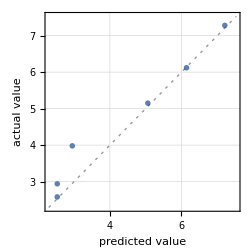
Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 6
Standard deviation | 0.456 ± 0.22
Standard deviation baseline | 1.68 ± 0.31
R-squared | 0.927 ± 0.075
Mean cross entropy | 0.644 ± 0.33
Single evaluation time | 1.7 ms/example
Batch evaluation speed | 347. examples/s
-Graphics- |

0.278333

```mathematica
net = Predict[trainingData,Method->"NearestNeighbors"]
PredictorMeasurements[net,noVescVariableVol]
%["MeanDeviation"]
```

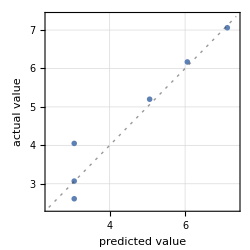
Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 6
Standard deviation | 0.451 ± 0.2
Standard deviation baseline | 1.6 ± 0.27
R-squared | 0.921 ± 0.074
Mean cross entropy | 0.636 ± 0.3
Single evaluation time | 1.79 ms/example
Batch evaluation speed | 354. examples/s
-Graphics- |

0.293333

```mathematica
PredictorMeasurements[net,vescSameVol]
%["MeanDeviation"]
```

Observation:  A simple nearest-neighbor classifier is decent for pH>5 even if the volume varies or vesicles are present.

### Optimal Transport Classifier

Try an optimal transport classifier (my favorite):

```mathematica
ot = Nearest[trainingData,DistanceFunction->emd]
```

NearestFunction[…]

This is fast with this limited amount of data:

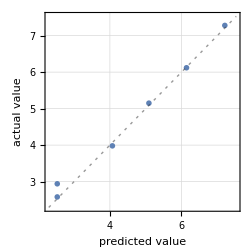
Predictor Measurements
Number of test examples | 6
Standard deviation | 0.177 ± 0.09
Standard deviation baseline | 1.68 ± 0.31
R-squared | 0.989 ± 0.012
-Graphics- |

```mathematica
With[
{pred=Flatten@ParallelMap[ot,noVescVariableVol[[All,1]]],
obs = noVescVariableVol[[All,2]]},
PredictorMeasurements[pred,obs]]
```

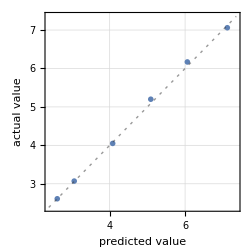
Predictor Measurements
Number of test examples | 6
Standard deviation | 0.0693 ± 0.018
Standard deviation baseline | 1.6 ± 0.27
R-squared | 0.998 ± 0.0012
-Graphics- |

```mathematica
With[
{pred=Flatten@ParallelMap[ot,vescSameVol[[All,1]]],
obs = vescSameVol[[All,2]]},
PredictorMeasurements[pred,obs]]
```

Observation:  The optimal transport (Earth Mover Distance) predictor is even better than nearest neighbors.  We can essentially get everything right with or without vesicles or constant volume.  Performance for the lowest pHs (<3) gets bad for variable volume, but this is because the spectra are hard to distinguish. Performance is perfect for all pHs in the presence of vesicles.